# Caso 2: Modelado de protocolos ARQ para análisis de rendimiento

```mathematica
Clear["Global`*"];
```

```mathematica
<<"/home/david/Documentos/RRT/RandomData.m"
<<"/home/david/Documentos/RRT/drawTx.m"
```

```mathematica
?drawTx`*
```

SetIniParDraw[propagation_time,ack_time] to configure parameters of transmission

Apartado 1
Estudiar librería de representación de paquetes y averiguar el formato del paquete
mu=C/l donde mu es en paq/s, l es bits/paquete y C es bits/segundo
DrawWin: para dibujar una ventana temporal 
DrawPacket: para dibujar los paquetes
SetIniParDraw[prop_time,ack_time]: configura parámetros de transmisión
Paquete = {tiempo_llegada, tasa_servicio*9600, num_sec, error, num_rep} en tasa de servicio 9600 equivale a un segundo y es el valor por defecto.

Apartado 2
Probar la representación de la librería para un caso particular de Stop & Wait sin errores y con tiempo de propagación 0. Posteriormente hacerlo proporcionando otros valores a cada parámetro

```mathematica
SetIniParDraw[0,10]
```

```mathematica
GetIniParDraw[];
```

```mathematica
packet={10,9600,7,0,0};
```

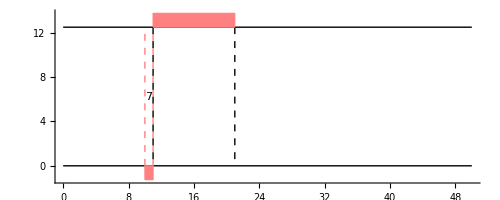

```mathematica
Show[DrawWin[0,50,10],DrawPacketTx[packet]]
```